#### IMEX BDF2 respecto a μ

El método IMEX BDF2 tiene la forma: 3/2y_(n+2)-2y_(n+1)+1/2y_n= -h*λ*y_(n+2)+h*γ*(2 y_(n+1-m)-y_(n-m))

Los coeficientes son α_2=3/2, α_2=-2, α_2=1/2, β_2=1, β_1=β_0=0, β_1^*=2, β_0^*=-1, γ_1=2, γ_0=-1. Así tendremos los polinomios y la ecuación característica, tomando m=0 como:

```mathematica
m=0;
ν=2; (*Este es el número de pasos del método*)
p[ξ_]:=3/2*ξ^2-2*ξ+1/2;
σ[ξ_]:=ξ^2;
SuperStar[σ][ξ_]:=2*ξ^(1-m)-ξ^-m;
eq[ξ_,z_,μ_]:=ξ^m*(p[ξ]-z*σ[ξ])+z*μ*SuperStar[σ][ξ];
Clear[z];
Solve[eq[E^(I*θ),z,μ]==0,μ]
```

{{μ→(-1+4 ⅇ^(ⅈ θ)-3 ⅇ^(2 ⅈ θ)+2 ⅇ^(2 ⅈ θ) z)/(2 (-1+2 ⅇ^(ⅈ θ)) z)}}

Con esto tenemos el conjunto de puntos (z,zμ) tales que la raíz ξ tiene exactamente módulo 1, es decir, es el conjunto de puntos de la curva que delimita la región de estabilidad. Así, dibujamos la parte real (eje X) e imaginaria (eje Y) de μ, respecto a varios z negativos.

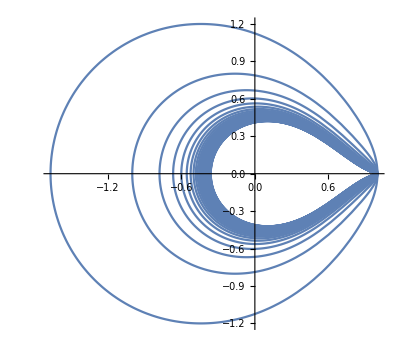

```mathematica
ParametricPlot[Table[ReIm[(-1+4 ⅇ^(ⅈ θ)-3 ⅇ^(2 ⅈ θ)+2 ⅇ^(2 ⅈ θ) z)/(2 (-1+2 ⅇ^(ⅈ θ)) z)],{z,-50,-1,1}],{θ,0,2Pi}]
```

```mathematica
ParametricPlot3D[{z, Re[(-1+4 ⅇ^(ⅈ θ)-3 ⅇ^(2 ⅈ θ)+2 ⅇ^(2 ⅈ θ) z)/(2 (-1+2 ⅇ^(ⅈ θ)) z)],Im[(-1+4 ⅇ^(ⅈ θ)-3 ⅇ^(2 ⅈ θ)+2 ⅇ^(2 ⅈ θ) z)/(2 (-1+2 ⅇ^(ⅈ θ)) z)]},{z,-10,-1},{θ,0,2Pi}]
```

-Graphics3D-

Se puede observar que la función de curva es simétrica en el eje horizontal: tanto para θ como para -θ, la parte real es igual debido a que la función Cos[] es par, es decir Cos[θ]=Cos[-θ], y la parte imaginaria es la misma en módulo pero con signo opuesto, debido a que Sin[] es impar, esto es Sin[-θ]=-Sin[θ]

```mathematica
curva[θ_]:=ExpToTrig[(-1+4 ⅇ^(ⅈ θ)-3 ⅇ^(2 ⅈ θ)+2 ⅇ^(2 ⅈ θ) z)/(2 (-1+2 ⅇ^(ⅈ θ)) z)];
curva[θ]
curva[-θ]
```

(-1+4 Cos[θ]-3 Cos[2 θ]+2 z Cos[2 θ]+4 ⅈ Sin[θ]-3 ⅈ Sin[2 θ]+2 ⅈ z Sin[2 θ])/(2 z (-1+2 Cos[θ]+2 ⅈ Sin[θ]))

(-1+4 Cos[θ]-3 Cos[2 θ]+2 z Cos[2 θ]-4 ⅈ Sin[θ]+3 ⅈ Sin[2 θ]-2 ⅈ z Sin[2 θ])/(2 z (-1+2 Cos[θ]-2 ⅈ Sin[θ]))

Veamos la región de estabilidad cuando z->-∞

```mathematica
Limit[ReIm[(-1+4 ⅇ^(ⅈ θ)-3 ⅇ^(2 ⅈ θ)+2 ⅇ^(2 ⅈ θ) z)/(2 (-1+2 ⅇ^(ⅈ θ)) z)],z->-Infinity]
```

{(ⅇ^(-Im[θ]) (2 Cos[Re[θ]]-ⅇ^Im[θ] Cos[2 Re[θ]]))/(4+ⅇ^(2 Im[θ])-4 ⅇ^Im[θ] Cos[Re[θ]]),(-2 Sin[θ]+Sin[2 θ])/(-5+4 Cos[θ])}

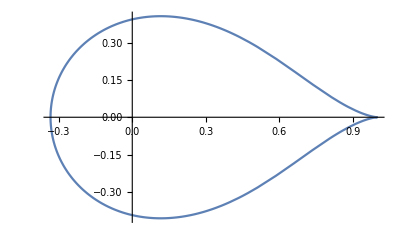

```mathematica
ParametricPlot[{(ⅇ^(-Im[θ]) (2 Cos[Re[θ]]-ⅇ^Im[θ] Cos[2 Re[θ]]))/(4+ⅇ^(2 Im[θ])-4 ⅇ^Im[θ] Cos[Re[θ]]),(-2 Sin[θ]+Sin[2 θ])/(-5+4 Cos[θ])},{θ,0,2Pi}]
```

En este sentido la región de estabilidad del BDF2 respecto a μ es todo el plano interior a la figura anterior

El punto exacto a la izquierda de esta gráfica es:

```mathematica
θ=Pi;
Solve[{(ⅇ^(-Im[θ]) (2 Cos[Re[θ]]-ⅇ^Im[θ] Cos[2 Re[θ]]))/(4+ⅇ^(2 Im[θ])-4 ⅇ^Im[θ] Cos[Re[θ]])==x,(-2 Sin[θ]+Sin[2 θ])/(-5+4 Cos[θ])==0},x]
```

{{x→-1/3}}

Calculemos ahora las raíces de la ecuación característica para comprobar si la región de estabilidad es fuera o dentro de lo representado

```mathematica
Solve[eq[ξ,z,μ]==0,ξ]
```

{{ξ→(-2+2 z μ-√(1+2 z-2 z μ-4 z^2 μ+4 z^2 μ^2))/(-3+2 z)},{ξ→(-2+2 z μ+√(1+2 z-2 z μ-4 z^2 μ+4 z^2 μ^2))/(-3+2 z)}}

```mathematica
Abs[{(-2+2 z μ-√(1+2 z-2 z μ-4 z^2 μ+4 z^2 μ^2))/(-3+2 z),(-2+2 z μ+√(1+2 z-2 z μ-4 z^2 μ+4 z^2 μ^2))/(-3+2 z)}]/.{z->-2,μ->-1.5} (*Aquí estamos poniendo por ejemplo el z=-2, es decir, la segunda región más exterior de la primera gráfica y tomando μ=-1.5 (fuera de la región) estamos comprobando si las raices verifican ser en módulo menores que 1, al no ser así indica que la región de estabilidad es el interior*)
```

{0.448775,1.59163}

Vamos a comprobar ahora dónde se encuentra σ_z, es decir, punto de la curva con menor distancia al centro del plano. Primero representamos la curva como función que depende de senos y cosenos:

```mathematica
ComplexExpand[(-1+4 ⅇ^(ⅈ θ)-3 ⅇ^(2 ⅈ θ)+2 ⅇ^(2 ⅈ θ) z)/(2 (-1+2 ⅇ^(ⅈ θ)) z)]
```

1/(2 z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))-(3 Cos[θ])/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))+(4 Cos[θ]^2)/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))-Cos[2 θ]/((-1+2 Cos[θ])^2+4 Sin[θ]^2)+(3 Cos[2 θ])/(2 z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))+(2 Cos[θ] Cos[2 θ])/((-1+2 Cos[θ])^2+4 Sin[θ]^2)-(3 Cos[θ] Cos[2 θ])/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))+(4 Sin[θ]^2)/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))+(2 Sin[θ] Sin[2 θ])/((-1+2 Cos[θ])^2+4 Sin[θ]^2)-(3 Sin[θ] Sin[2 θ])/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))+ⅈ (-Sin[θ]/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))-(2 Cos[2 θ] Sin[θ])/((-1+2 Cos[θ])^2+4 Sin[θ]^2)+(3 Cos[2 θ] Sin[θ])/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))-Sin[2 θ]/((-1+2 Cos[θ])^2+4 Sin[θ]^2)+(3 Sin[2 θ])/(2 z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))+(2 Cos[θ] Sin[2 θ])/((-1+2 Cos[θ])^2+4 Sin[θ]^2)-(3 Cos[θ] Sin[2 θ])/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2)))

La función distancia al cuadrado (lo ponemos al cuadrado para evitar raíces cuadradas y luego al tomar el valor de la función pondremos la raíz cuadrada) es:

```mathematica
Simplify[(1/(2 z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))-(3 Cos[θ])/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))+(4 Cos[θ]^2)/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))-Cos[2 θ]/((-1+2 Cos[θ])^2+4 Sin[θ]^2)+(3 Cos[2 θ])/(2 z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))+(2 Cos[θ] Cos[2 θ])/((-1+2 Cos[θ])^2+4 Sin[θ]^2)-(3 Cos[θ] Cos[2 θ])/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))+(4 Sin[θ]^2)/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))+(2 Sin[θ] Sin[2 θ])/((-1+2 Cos[θ])^2+4 Sin[θ]^2)-(3 Sin[θ] Sin[2 θ])/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2)))^2+(-Sin[θ]/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))-(2 Cos[2 θ] Sin[θ])/((-1+2 Cos[θ])^2+4 Sin[θ]^2)+(3 Cos[2 θ] Sin[θ])/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))-Sin[2 θ]/((-1+2 Cos[θ])^2+4 Sin[θ]^2)+(3 Sin[2 θ])/(2 z ((-1+2 Cos[θ])^2+4 Sin[θ]^2))+(2 Cos[θ] Sin[2 θ])/((-1+2 Cos[θ])^2+4 Sin[θ]^2)-(3 Cos[θ] Sin[2 θ])/(z ((-1+2 Cos[θ])^2+4 Sin[θ]^2)))^2]
```

(13-6 z+2 z^2+8 (-2+z) Cos[θ]+(3-2 z) Cos[2 θ])/(2 z^2 (5-4 Cos[θ]))

```mathematica
FuncDistCuad[z_,θ_]:=(13-6 z+2 z^2+8 (-2+z) Cos[θ]+(3-2 z) Cos[2 θ])/(2 z^2 (5-4 Cos[θ]));
```

Para calcular los puntos con distancia mínima, es decir, los mínimos de la función, tenemos en cuenta que serán ceros de la derivada de esta última función:

```mathematica
Simplify[D[FuncDistCuad[z,θ],θ]]
```

-(2 (-13+8 z+2 z^2-5 (-3+2 z) Cos[θ]+(-3+2 z) Cos[2 θ]) Sin[θ])/(z^2 (5-4 Cos[θ])^2)

```mathematica
Assuming[  z<0&&0≤ θ≤ Pi, Reduce[  -(2 (-13+8 z+2 z^2-5 (-3+2 z) Cos[θ]+(-3+2 z) Cos[2 θ]) Sin[θ])/(z^2 (5-4 Cos[θ])^2)==0, θ] ]
```

(C[1]∈ℤ&&((z==1/2 (-10-9 √2)&&θ==π+2 π C[1])||(z==1/2 (-10+9 √2)&&θ==π+2 π C[1])||(z≠0&&(θ==2 π C[1]||θ==π+2 π C[1]))))||(C[1]∈ℤ&&z==1/2 (-10-9 √2)&&(θ==-2 ⅈ ArcTanh[(√5)/3]+2 π C[1]||θ==2 ⅈ ArcTanh[(√5)/3]+2 π C[1]))||(C[1]∈ℤ&&z==1/2 (-10+9 √2)&&(θ==-2 ⅈ ArcTanh[(√5)/3]+2 π C[1]||θ==2 ⅈ ArcTanh[(√5)/3]+2 π C[1]))||(C[1]∈ℤ&&-31+20 z+2 z^2≠0&&((z (135-36 z-468 z^2+288 z^3-119 √(-15+4 z+52 z^2-32 z^3)+82 z √(-15+4 z+52 z^2-32 z^3)-8 z^2 √(-15+4 z+52 z^2-32 z^3))≠0&&(θ==-2 ArcTan[√((4-2 z-2 z^2-√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))]+2 π C[1]||θ==2 ArcTan[√((4-2 z-2 z^2-√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))]+2 π C[1]))||(z (135-36 z-468 z^2+288 z^3+119 √(-15+4 z+52 z^2-32 z^3)-82 z √(-15+4 z+52 z^2-32 z^3)+8 z^2 √(-15+4 z+52 z^2-32 z^3))≠0&&(θ==-2 ArcTan[√((4-2 z-2 z^2+√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))]+2 π C[1]||θ==2 ArcTan[√((4-2 z-2 z^2+√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))]+2 π C[1]))))

Los ángulos devueltos de manera general son:    θ=0;    θ=Pi;     θ=±2 ⅈ ArcTanh[(√5)/3]=±1.92485 ⅈ;     θ=±2 ArcTan[√((4-2 z-2 z^2-√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))];        θ=2 ArcTan[√((4-2 z-2 z^2+√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))]
Los valores complejos no nos interesan, ya que consideramos 0≤θ≤Pi, por lo que descartamos el tercer resultado. Sustituimos estos valores de θ en la función distancia minima (FuncDistCuad) y veamos dónde se toman los valores mínimos:

```mathematica
FullSimplify[FuncDistCuad[z,θ]/.{θ->0}]
```

1

```mathematica
FullSimplify[Sqrt[FuncDistCuad[z,θ]/.{θ->Pi}], z<0]
```

(-4+z)/(3 z)

```mathematica
FullSimplify[Sqrt[FuncDistCuad[z,θ]/.{θ->2 ArcTan[√((4-2 z-2 z^2-√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))]}],z<0]
```

-(√(1+2 z+√(-(-3+2 z) (1+2 z) (-5+8 z))))/(2 √2 z)

```mathematica
FullSimplify[Sqrt[FuncDistCuad[z,θ]/.{θ->-2 ArcTan[√((4-2 z-2 z^2-√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))]}],z<0]
```

-(√(1+2 z+√(-(-3+2 z) (1+2 z) (-5+8 z))))/(2 √2 z)

```mathematica
Table[{-2 ArcTan[√((4-2 z-2 z^2-√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))],z},{z,-50.1,-0.1}] (*Se observa que θ=-2 ArcTan[√((4-2 z-2 z^2-√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))] para valores entre, más o menos -12.1 y -0.1 posee valores reales, que son los que nos interesan. Veamos concretamente cuáles son*)
```

{{-3.14159-1.9792 ⅈ,-50.1},{-3.14159-1.96476 ⅈ,-49.1},{-3.14159-1.94995 ⅈ,-48.1},{-3.14159-1.93474 ⅈ,-47.1},{-3.14159-1.91912 ⅈ,-46.1},{-3.14159-1.90306 ⅈ,-45.1},{-3.14159-1.88653 ⅈ,-44.1},{-3.14159-1.86952 ⅈ,-43.1},{-3.14159-1.85199 ⅈ,-42.1},{-3.14159-1.83391 ⅈ,-41.1},{-3.14159-1.81524 ⅈ,-40.1},{-3.14159-1.79595 ⅈ,-39.1},{-3.14159-1.77599 ⅈ,-38.1},{-3.14159-1.75532 ⅈ,-37.1},{-3.14159-1.73389 ⅈ,-36.1},{-3.14159-1.71164 ⅈ,-35.1},{-3.14159-1.68851 ⅈ,-34.1},{-3.14159-1.66442 ⅈ,-33.1},{-3.14159-1.63929 ⅈ,-32.1},{-3.14159-1.61304 ⅈ,-31.1},{-3.14159-1.58556 ⅈ,-30.1},{-3.14159-1.55674 ⅈ,-29.1},{-3.14159-1.52643 ⅈ,-28.1},{-3.14159-1.49448 ⅈ,-27.1},{-3.14159-1.46071 ⅈ,-26.1},{-3.14159-1.42489 ⅈ,-25.1},{-3.14159-1.38677 ⅈ,-24.1},{-3.14159-1.34604 ⅈ,-23.1},{-3.14159-1.30231 ⅈ,-22.1},{-3.14159-1.2551 ⅈ,-21.1},{-3.14159-1.20382 ⅈ,-20.1},{-3.14159-1.14768 ⅈ,-19.1},{-3.14159-1.08564 ⅈ,-18.1},{-3.14159-1.01626 ⅈ,-17.1},{-3.14159-0.937445 ⅈ,-16.1},{-3.14159-0.845959 ⅈ,-15.1},{-3.14159-0.736244 ⅈ,-14.1},{-3.14159-0.59707 ⅈ,-13.1},{-3.14159-0.396294 ⅈ,-12.1},{-2.89933,-11.1},{-2.59952,-10.1},{-2.39826,-9.1},{-2.22484,-8.1},{-2.06201,-7.1},{-1.9008,-6.1},{-1.73399,-5.1},{-1.55317,-4.1},{-1.3449,-3.1},{-1.07944,-2.1},{-0.637035,-1.1},{-0.350011-0.792351 ⅈ,-0.1}}

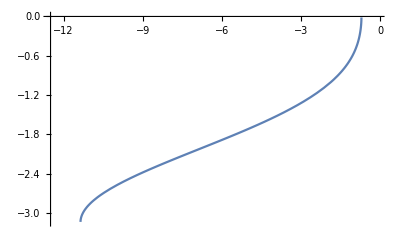

```mathematica
Plot[-2 ArcTan[√((4-2 z-2 z^2-√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))],{z,-12.5,-0.1}]
```

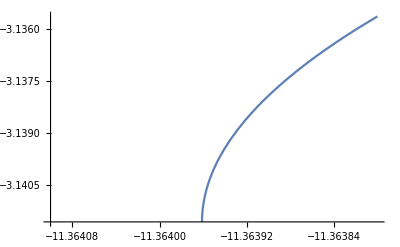

```mathematica
Plot[-2 ArcTan[√((4-2 z-2 z^2-√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))],{z,-11.3641,-11.3638}]
```

Entre -11.364 ≤ z ≤ -1/(√2), el θ=-2 ArcTan[√((4-2 z-2 z^2-√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))], se corresponde con números reales, el resto, complejos, lo cual no nos sirve

```mathematica
Reduce[-2 ArcTan[√((4-2 z-2 z^2-√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))]==0&&z<0,z]
```

z==-1/(√2)

```mathematica
FullSimplify[Sqrt[FuncDistCuad[z,θ]/.{θ->2 ArcTan[√((4-2 z-2 z^2+√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))]}],z<0]
```

-(√(1/2+z-1/2 √(-(-3+2 z) (1+2 z) (-5+8 z))))/(2 z)

```mathematica
FullSimplify[Sqrt[FuncDistCuad[z,θ]/.{θ->-2 ArcTan[√((4-2 z-2 z^2+√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))]}],z<0]
```

-(√(1/2+z-1/2 √(-(-3+2 z) (1+2 z) (-5+8 z))))/(2 z)

```mathematica
Table[-2 ArcTan[√((4-2 z-2 z^2+√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))],{z,-50.1,-0.1}] (*esto indica que θ=-(√(1/2+z-1/2 √(-(-3+2 z) (1+2 z) (-5+8 z))))/(2 z) es complejo para z<0, tampoco nos interesa*)
```

{0.-2.50909 ⅈ,0.-2.50073 ⅈ,0.-2.4922 ⅈ,0.-2.48351 ⅈ,0.-2.47465 ⅈ,0.-2.4656 ⅈ,0.-2.45636 ⅈ,0.-2.44693 ⅈ,0.-2.43729 ⅈ,0.-2.42744 ⅈ,0.-2.41736 ⅈ,0.-2.40704 ⅈ,0.-2.39648 ⅈ,0.-2.38565 ⅈ,0.-2.37455 ⅈ,0.-2.36316 ⅈ,0.-2.35147 ⅈ,0.-2.33945 ⅈ,0.-2.32709 ⅈ,0.-2.31437 ⅈ,0.-2.30126 ⅈ,0.-2.28774 ⅈ,0.-2.27379 ⅈ,0.-2.25936 ⅈ,0.-2.24444 ⅈ,0.-2.22897 ⅈ,0.-2.21292 ⅈ,0.-2.19625 ⅈ,0.-2.17889 ⅈ,0.-2.16079 ⅈ,0.-2.14188 ⅈ,0.-2.12208 ⅈ,0.-2.10129 ⅈ,0.-2.07941 ⅈ,0.-2.05632 ⅈ,0.-2.03186 ⅈ,0.-2.00585 ⅈ,0.-1.97808 ⅈ,0.-1.94828 ⅈ,0.-1.9161 ⅈ,0.-1.88112 ⅈ,0.-1.84278 ⅈ,0.-1.80031 ⅈ,0.-1.75269 ⅈ,0.-1.69839 ⅈ,0.-1.63511 ⅈ,0.-1.55907 ⅈ,0.-1.46339 ⅈ,0.-1.33307 ⅈ,0.-1.12042 ⅈ,-0.350011+0.792351 ⅈ}

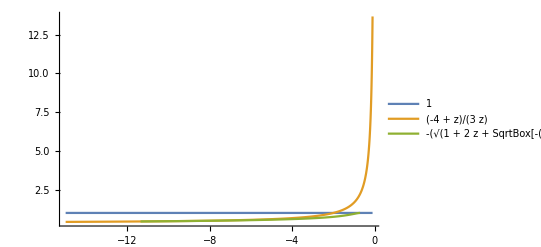

```mathematica
Plot[{1,(-4+z)/(3 z),If[1/2 (-10-9 √2)≤z≤-1/(√2),-(√(1+2 z+√(-(-3+2 z) (1+2 z) (-5+8 z))))/(2 √2 z)]},{z,-15,-0.1}, PlotLegends->{"1","(-4 + z)/(3  z)","-(√(1 + 2  z + SqrtBox[-(-3 + 2  z)  (1 + 2  z)  (-5 + 8  z)]))/(2  SqrtBox[2]  z)"}, PlotRange->All]
```

Veamos cuando una es mayor que otra:

```mathematica
Reduce[{1<(-4+z)/(3 z)&&z<0},z]
```

-2<z<0

```mathematica
Reduce[{-(√(1+2 z+√(-(-3+2 z) (1+2 z) (-5+8 z))))/(2 √2 z)<=(-4+z)/(3 z)&&z<0},z](*realmente la tercera función se define a partir de -1/(√2)=-0.70717, entonces es realmente válido esto para z<=-1/(√2)*)
```

z≤-1/2

```mathematica
N[1/2 (-10-9 √2)]
```

-11.364

```mathematica
Reduce[{-(√(1+2 z+√(-(-3+2 z) (1+2 z) (-5+8 z))))/(2 √2 z)<1&&z<0},z]
```

z<-1/(√2)||-1/(√2)<z≤-1/2

```mathematica
N[-1/(√2)]
```

-0.707107

```mathematica
Reduce[{-(√(1+2 z+√(-(-3+2 z) (1+2 z) (-5+8 z))))/(2 √2 z)==1&&z<0},z]
```

z==-1/(√2)

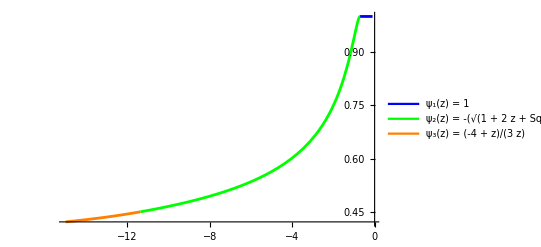

```mathematica
Plot[{If[z>=-1/(√2),1],If[z<=1/2 (-10-9 √2),(-4+z)/(3 z)],If[1/2 (-10-9 √2)≤z≤-1/(√2),-(√(1+2 z+√(-(-3+2 z) (1+2 z) (-5+8 z))))/(2 √2 z)]},{z,-15,-0.1}, PlotLegends->Placed[LineLegend[{Blue,Green,Orange},{"ψ_1(z) = 1","ψ_2(z) = -(√(1 + 2  z + SqrtBox[-(-3 + 2  z)  (1 + 2  z)  (-5 + 8  z)]))/(2  SqrtBox[2]  z)","ψ_3(z) = (-4 + z)/(3  z)"}],{0.3,0.7}], PlotRange->All, PlotStyle->{Blue,  Orange, Green}]
```

La conclusión es que para z∈[-1/(√2),0] la distancia mínima es σ_z=1, lo cual se obtiene con θ=0, para z∈[-1/2 (-10-9 √2),-1/(√2)], la distancia mínima se obtiene cuando θ=2 ArcTan[√((4-2 z-2 z^2-√(-15+4 z+52 z^2-32 z^3))/(-31+20 z+2 z^2))], y para  z∈[-∞, -1/2 (-10-9 √2)], el valor mínimo se alcanza para θ=Pi.

Cálculo de las derivadas de estas funciones

```mathematica
D[1,z]
```

0

```mathematica
FullSimplify[D[-(√(1+2 z+√(-(-3+2 z) (1+2 z) (-5+8 z))))/(2 √2 z),z]]
```

(-15+26 z^2-8 z^3+√(-15+4 z+52 z^2-32 z^3)+z (3+√(-15+4 z+52 z^2-32 z^3)))/(2 z^2 √(-30+8 z+104 z^2-64 z^3) √(1+2 z+√(-15+4 z+52 z^2-32 z^3)))

```mathematica
FullSimplify[D[(-4+z)/(3 z),z]]
```

4/(3 z^2)

Representación gráfica

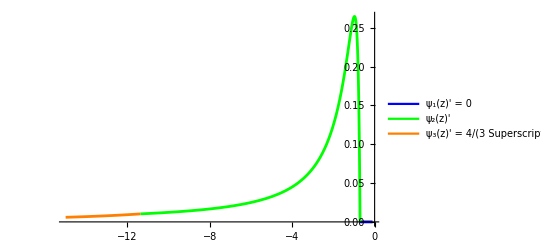

```mathematica
Plot[{If[z>=-1/(√2),0],If[z<=1/2 (-10-9 √2),4/(3 z^2)],If[1/2 (-10-9 √2)≤z≤-1/(√2),(-15+26 z^2-8 z^3+√(-15+4 z+52 z^2-32 z^3)+z (3+√(-15+4 z+52 z^2-32 z^3)))/(2 z^2 √(-30+8 z+104 z^2-64 z^3) √(1+2 z+√(-15+4 z+52 z^2-32 z^3)))]},{z,-15,-0.1}, PlotLegends->Placed[LineLegend[{Blue,Green,Orange},{"ψ_1(z)' = 0","ψ_2(z)'","ψ_3(z)' = 4/(3 SuperscriptBox[z, 2])"}],{0.2,0.7}], PlotRange->All, PlotStyle->{Blue,  Orange, Green}]
```

Comprobación de que la función de mínimos es continua

```mathematica
f1[z_]:=1;
f2[z_]:=(-√(1+2z+√(-(-3+2z)(1+2z)(-5+8z))))/(2z √2);
f3[z_]:=(-4+z)/(3z);
p1=-1/(√2);
p2=1/2(-10-9 √2);
```

```mathematica
N[Simplify[f2[p1]]](*Esto indica que es continua la función de mínimos*)
```

1.

```mathematica
N[Simplify[f2[p2]]]
```

0.450663

```mathematica
N[Simplify[f3[p2]]]
```

0.450663

La comprobación de que la función de mínimos es no decreciente:

```mathematica
Solve[D[-(√(1+2 z+√(-(-3+2 z) (1+2 z) (-5+8 z))))/(2 √2 z),z]==0,z](*El único punto con pendiente nula es el extremo*)
```

{{z→-1/(√2)},{z→1/(√2)}}

```mathematica
Reduce[D[-(√(1+2 z+√(-(-3+2 z) (1+2 z) (-5+8 z))))/(2 √2 z),z]>0&&z<0](*En su dominio es creciente al ser la primera derivada positiva*)
```

z<-1/(√2)

```mathematica
Solve[D[(-4+z)/(3 z),z]==0,z](*Nunca ocurre que se anule*)
```

{}

```mathematica
Reduce[D[(-4+z)/(3 z),z]>0&&z<0](*En su dominio es creciente al ser la primera derivada positiva*)
```

z<0

Cálculo de las inversas de las funciones que forman la función de mínimos

```mathematica
Reduce[f2[z]==r&&z<0&&3/31 (-1+4 √2)<r≤1,z]
```

(1/31 (-3+12 √2)<r<1&&(z==Root[1+(-3-r^2) #1^2+(2-2 r^2) #1^3+4 r^4 #1^4&,1]||z==Root[1+(-3-r^2) #1^2+(2-2 r^2) #1^3+4 r^4 #1^4&,2]))||(r==1&&z==-1/(√2))

```mathematica
(*Funciones inversas de la función del segundo tramo*)
f21[r_]:=Solve[1+(-3-r^2) #1^2+(2-2 r^2) #1^3+4 r^4 #1^4==0,#1][[1]][[1]][[2]]
f22[r_]:=Solve[1+(-3-r^2) #1^2+(2-2 r^2) #1^3+4 r^4 #1^4==0,#1][[2]][[1]][[2]]
```

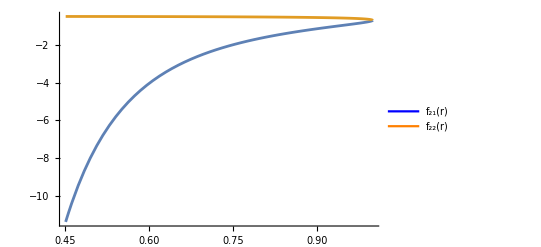

```mathematica
Plot[{f21[r],f22[r]},{r,3/31 (-1+4 √2),1}, PlotRange->All, PlotLegends->Placed[LineLegend[{Blue, Orange},{"f_21(r)","f_22(r)"}],{0.8,0.2}]]
```

```mathematica
Plot[f21[r],{r,3/31 (-1+4 √2),1}]
```

```mathematica
Plot[f22[r],{r,3/31 (-1+4 √2),1}](*Se ve que esta función, para los valores de z que devuelve no es la adecuada*)
```

```mathematica
FullSimplify[Solve[f3[z]==r,z]](*Función inversa de la función del tercer tramo*)
```

{{z→4/(1-3 r)}}

Sea ahora la comprobación numérica de lo calculado anteriormente:

```mathematica
listminimos={};
circ={};
For[j=0,j≤49,j++;
z=-j;
lista=Table[Sqrt[Re[(-1+4 ⅇ^(ⅈ θ)-3 ⅇ^(2 ⅈ θ)+2 ⅇ^(2 ⅈ θ) z)/(2 (-1+2 ⅇ^(ⅈ θ)) z)]^2+Im[(-1+4 ⅇ^(ⅈ θ)-3 ⅇ^(2 ⅈ θ)+2 ⅇ^(2 ⅈ θ) z)/(2 (-1+2 ⅇ^(ⅈ θ)) z)]^2],{θ,0,Pi,0.01}];
AppendTo[circ,{Min[lista]*Cos[t],Min[lista]*Sin[t]}];
pos=Position[lista,Min[lista]][[1]][[1]];
α=0.01*(pos-1);
AppendTo[listminimos,ReIm[(-1+4 ⅇ^(ⅈ α)-3 ⅇ^(2 ⅈ α)+2 ⅇ^(2 ⅈ α) z)/(2 (-1+2 ⅇ^(ⅈ α))z)]];
];
minimos=ListPlot[listminimos, PlotStyle->Red, PlotLegends->Placed[LineLegend[{Red},{"σ_z"}],{0.065,0.18}]];
regest=ParametricPlot[Table[ReIm[(-1+4 ⅇ^(ⅈ θ)-3 ⅇ^(2 ⅈ θ)+2 ⅇ^(2 ⅈ θ) z)/(2 (-1+2 ⅇ^(ⅈ θ)) z)],{z,-50,-1,1}],{θ,0,2Pi}, PlotLegends->Placed[LineLegend[{Blue,Yellow},{"Regiones","D(0,σ_z)"}],{0.1,0.08}]];
circulos=ParametricPlot[circ,{t,0,2Pi}, PlotStyle->Yellow];
Show[circulos,regest,minimos, PlotRange->All, PlotLabel->"Regiones de estabilidad IMEX-BDF2, m=0"]
```

Efectivamente, como hemos comprobado analíticamente, para z≤-11.34 se tiene que la distancia mínima se alcanza para θ=Pi.

Comprobaremos que para m>0, las regiones de estabilidad azules se aproximan a las amarillas (que representan círculos de radio igual a la distancia mínima de cada curva)

```mathematica
m=1;
p[ξ_]:=3/2*ξ^2-2*ξ+1/2;
σ[ξ_]:=ξ^2;
SuperStar[σ][ξ_]:=2*ξ^(1-m)-ξ^-m;
eq[ξ_,z_,μ_]:=ξ^m*(p[ξ]-z*σ[ξ])+z*μ*SuperStar[σ][ξ];

listminimos={};
circ={};
For[j=0,j≤14,j++;
z=-j;
lista=Table[Sqrt[Re[Solve[eq[E^(I*θ),z,μ]==0,μ][[1]][[1]][[2]]]^2+Im[Solve[eq[E^(I*θ),z,μ]==0,μ][[1]][[1]][[2]]]^2],{θ,0,Pi,0.01}];
AppendTo[circ,{Min[lista]*Cos[t],Min[lista]*Sin[t]}];
pos=Position[lista,Min[lista]][[1]][[1]];
α=0.01*(pos-1);
AppendTo[listminimos,ReIm[Solve[eq[E^(I*α),z,μ]==0,μ][[1]][[1]][[2]]]];
];
minimos=ListPlot[listminimos, PlotStyle->Red, PlotLegends->LineLegend[{Red},{"σ_z"}]];
regest=ParametricPlot[Table[ReIm[Solve[eq[E^(I*θ),z,μ]==0,μ][[1]][[1]][[2]]],{z,-15,-1,1}],{θ,0,2Pi}, PlotLegends->LineLegend[{Blue,Yellow},{"Regiones","D(0,σ_z)"}]];
circulos=ParametricPlot[circ,{t,0,2Pi}, PlotStyle->Yellow];
Show[circulos,regest,minimos, PlotRange->All, PlotLabel->"Regiones de estabilidad IMEX-BDF2, m=1"]
```

Veamos, por ejemplo, para un z fijo (z=-1) que aumentando m, la región de estabilidad (que se corresponde con el interior de los círculos dibujados) se aproxima cada vez más a la región formada por el círculo de radio la distancia mínima:

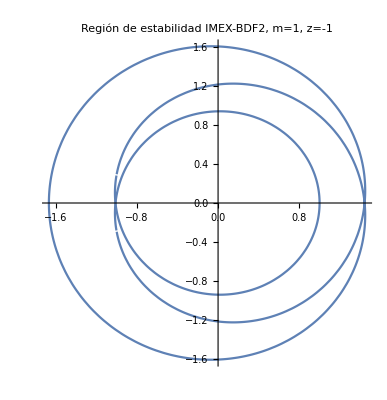

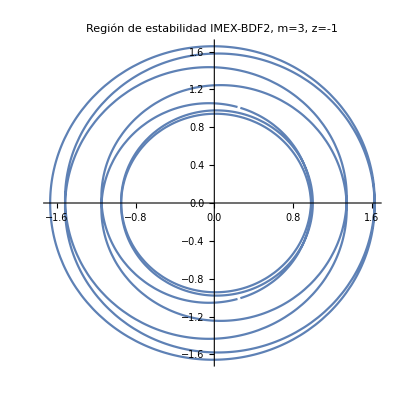

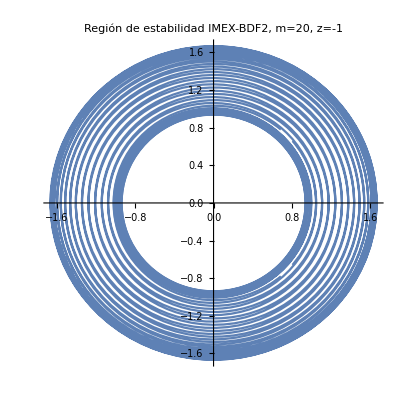

```mathematica
m=1;
p[ξ_]:=3/2*ξ^2-2*ξ+1/2;
σ[ξ_]:=ξ^2;
SuperStar[σ][ξ_]:=2*ξ^(1-m)-ξ^-m;
eq[ξ_,z_,μ_]:=ξ^m*(p[ξ]-z*σ[ξ])+z*μ*SuperStar[σ][ξ];

z=-1;

regest=ParametricPlot[ReIm[Solve[eq[E^(I*θ),z,μ]==0,μ][[1]][[1]][[2]]],{θ,0,2Pi}];
Show[regest, PlotRange->All, PlotLabel->"Región de estabilidad IMEX-BDF2, m=1, z=-1"]

m=3;
p[ξ_]:=3/2*ξ^2-2*ξ+1/2;
σ[ξ_]:=ξ^2;
SuperStar[σ][ξ_]:=2*ξ^(1-m)-ξ^-m;
eq[ξ_,z_,μ_]:=ξ^m*(p[ξ]-z*σ[ξ])+z*μ*SuperStar[σ][ξ];

z=-1;

regest=ParametricPlot[ReIm[Solve[eq[E^(I*θ),z,μ]==0,μ][[1]][[1]][[2]]],{θ,0,2Pi}];
Show[regest, PlotRange->All, PlotLabel->"Región de estabilidad IMEX-BDF2, m=3, z=-1"]

m=20;
p[ξ_]:=3/2*ξ^2-2*ξ+1/2;
σ[ξ_]:=ξ^2;
SuperStar[σ][ξ_]:=2*ξ^(1-m)-ξ^-m;
eq[ξ_,z_,μ_]:=ξ^m*(p[ξ]-z*σ[ξ])+z*μ*SuperStar[σ][ξ];

z=-1;

regest=ParametricPlot[ReIm[Solve[eq[E^(I*θ),z,μ]==0,μ][[1]][[1]][[2]]],{θ,0,2Pi}];
Show[regest, PlotRange->All, PlotLabel->"Región de estabilidad IMEX-BDF2, m=20, z=-1"]
```

Consistencia del método IMEX BDF2

```mathematica
(*Las condiciones son las salidas de los códigos inmediatamente anteriores*)
```

```mathematica
z[tn_]:= Series[ f[tn,y[tn]]+g[tn,y[tn],y[tn-m h]],{h,0,3}];
```

```mathematica
Simplify[  Series[ ( Series[ z[tn],{h,0,3}] /.{y'''[tn]->z''[tn]}  /.{y''[tn]->z'[tn]} /.{y'[tn]->z[tn]}  ),{h,0,3}] /.{y'''[tn]->z''[tn]}  /.{y''[tn]->z'[tn]} /.{y'[tn]->z[tn]}    ]
```

```mathematica
condicion1=(f[tn,y[tn]]+g[tn,y[tn],y[tn]])-m (f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,0,1][g][tn,y[tn],y[tn]] h+1/2 m^2 (2 (f[tn,y[tn]]+g[tn,y[tn],y[tn]]) (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2+(f[tn,y[tn]]+g[tn,y[tn],y[tn]])^2 Derivative[0,0,2][g][tn,y[tn],y[tn]]+Derivative[0,0,1][g][tn,y[tn],y[tn]] ((f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,1][f][tn,y[tn]]+Derivative[1,0][f][tn,y[tn]]+(f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,0,1][g][tn,y[tn],y[tn]]+(f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,1,0][g][tn,y[tn],y[tn]]+Derivative[1,0,0][g][tn,y[tn],y[tn]])) h^2-1/6 (m^3 (f[tn,y[tn]]^3 Derivative[0,0,3][g][tn,y[tn],y[tn]]+g[tn,y[tn],y[tn]]^3 Derivative[0,0,3][g][tn,y[tn],y[tn]]+g[tn,y[tn],y[tn]]^2 (Derivative[0,2][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+3 Derivative[0,1][f][tn,y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+16 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+3 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+5 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,2,0][g][tn,y[tn],y[tn]])+f[tn,y[tn]]^2 (Derivative[0,2][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+3 Derivative[0,1][f][tn,y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+16 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+3 g[tn,y[tn],y[tn]] Derivative[0,0,3][g][tn,y[tn],y[tn]]+3 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+5 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,2,0][g][tn,y[tn],y[tn]])+g[tn,y[tn],y[tn]] ((Derivative[0,1][f][tn,y[tn]])^2 Derivative[0,0,1][g][tn,y[tn],y[tn]]+2 Derivative[1,1][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+10 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^3+3 Derivative[1,0][f][tn,y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+11 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2 Derivative[0,1,0][g][tn,y[tn],y[tn]]+Derivative[0,0,1][g][tn,y[tn],y[tn]] (Derivative[0,1,0][g][tn,y[tn],y[tn]])^2+Derivative[0,1][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]] (11 Derivative[0,0,1][g][tn,y[tn],y[tn]]+2 Derivative[0,1,0][g][tn,y[tn],y[tn]])+3 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+5 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,0,1][g][tn,y[tn],y[tn]]+2 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,1,0][g][tn,y[tn],y[tn]])+f[tn,y[tn]] ((Derivative[0,1][f][tn,y[tn]])^2 Derivative[0,0,1][g][tn,y[tn],y[tn]]+2 Derivative[1,1][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+10 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^3+3 Derivative[1,0][f][tn,y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+3 g[tn,y[tn],y[tn]]^2 Derivative[0,0,3][g][tn,y[tn],y[tn]]+11 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2 Derivative[0,1,0][g][tn,y[tn],y[tn]]+Derivative[0,0,1][g][tn,y[tn],y[tn]] (Derivative[0,1,0][g][tn,y[tn],y[tn]])^2+Derivative[0,1][f][tn,y[tn]] (11 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2+6 g[tn,y[tn],y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+2 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]])+2 g[tn,y[tn],y[tn]] (Derivative[0,2][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+3 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+Derivative[0,0,1][g][tn,y[tn],y[tn]] (16 Derivative[0,0,2][g][tn,y[tn],y[tn]]+5 Derivative[0,1,1][g][tn,y[tn],y[tn]]+Derivative[0,2,0][g][tn,y[tn],y[tn]]))+3 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+5 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,0,1][g][tn,y[tn],y[tn]]+2 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,1,0][g][tn,y[tn],y[tn]])+Derivative[0,0,1][g][tn,y[tn],y[tn]] (Derivative[2,0][f][tn,y[tn]]+7 Derivative[1,0][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+6 y'[tn] (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2+Derivative[1,0][f][tn,y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+7 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+Derivative[0,1,0][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+Derivative[0,1][f][tn,y[tn]] (Derivative[1,0][f][tn,y[tn]]+Derivative[1,0,0][g][tn,y[tn],y[tn]])+Derivative[2,0,0][g][tn,y[tn],y[tn]]))) h^3;
```

```mathematica
Simplify[    Series[     Series[ z'[tn],{h,0,3}]/.{y'''[tn]->z''[tn]}  /.{y''[tn]->z'[tn]} /.y'[tn]->  condicion1   ,{h,0,2}]  /.{y'''[tn]->z''[tn]}  /.{y''[tn]->z'[tn]} /.y'[tn]->  condicion1  ]
```

```mathematica
condicion2=((f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,1][f][tn,y[tn]]+Derivative[1,0][f][tn,y[tn]]+(f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,0,1][g][tn,y[tn],y[tn]]+(f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,1,0][g][tn,y[tn],y[tn]]+Derivative[1,0,0][g][tn,y[tn],y[tn]])-m (f[tn,y[tn]]^2 (Derivative[0,0,2][g][tn,y[tn],y[tn]]+Derivative[0,1,1][g][tn,y[tn],y[tn]])+g[tn,y[tn],y[tn]]^2 (Derivative[0,0,2][g][tn,y[tn],y[tn]]+Derivative[0,1,1][g][tn,y[tn],y[tn]])+Derivative[0,0,1][g][tn,y[tn],y[tn]] (Derivative[1,0][f][tn,y[tn]]+Derivative[1,0,0][g][tn,y[tn],y[tn]])+g[tn,y[tn],y[tn]] (2 Derivative[0,1][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+2 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2+2 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+Derivative[1,0,1][g][tn,y[tn],y[tn]])+f[tn,y[tn]] (2 Derivative[0,1][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+2 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2+2 g[tn,y[tn],y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+2 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+2 g[tn,y[tn],y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+Derivative[1,0,1][g][tn,y[tn],y[tn]])) h+1/2 m^2 (2 Derivative[0,1][f][tn,y[tn]] Derivative[1,0][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+Derivative[2,0][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+4 Derivative[1,0][f][tn,y[tn]] (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2+2 Derivative[1,0][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+f[tn,y[tn]]^3 (Derivative[0,0,3][g][tn,y[tn],y[tn]]+Derivative[0,1,2][g][tn,y[tn],y[tn]])+g[tn,y[tn],y[tn]]^3 (Derivative[0,0,3][g][tn,y[tn],y[tn]]+Derivative[0,1,2][g][tn,y[tn],y[tn]])+2 Derivative[0,1][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+4 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2 Derivative[1,0,0][g][tn,y[tn],y[tn]]+2 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+Derivative[1,0][f][tn,y[tn]] Derivative[1,0,1][g][tn,y[tn],y[tn]]+Derivative[1,0,0][g][tn,y[tn],y[tn]] Derivative[1,0,1][g][tn,y[tn],y[tn]]+g[tn,y[tn],y[tn]]^2 (Derivative[0,2][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+11 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+4 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+9 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+Derivative[0,1,0][g][tn,y[tn],y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+Derivative[0,1][f][tn,y[tn]] (4 Derivative[0,0,2][g][tn,y[tn],y[tn]]+Derivative[0,1,1][g][tn,y[tn],y[tn]])+Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,2,0][g][tn,y[tn],y[tn]]+Derivative[1,0,2][g][tn,y[tn],y[tn]])+f[tn,y[tn]]^2 (Derivative[0,2][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+11 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+3 g[tn,y[tn],y[tn]] Derivative[0,0,3][g][tn,y[tn],y[tn]]+4 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+9 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+Derivative[0,1,0][g][tn,y[tn],y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+Derivative[0,1][f][tn,y[tn]] (4 Derivative[0,0,2][g][tn,y[tn],y[tn]]+Derivative[0,1,1][g][tn,y[tn],y[tn]])+3 g[tn,y[tn],y[tn]] Derivative[0,1,2][g][tn,y[tn],y[tn]]+Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,2,0][g][tn,y[tn],y[tn]]+Derivative[1,0,2][g][tn,y[tn],y[tn]])+g[tn,y[tn],y[tn]] (2 (Derivative[0,1][f][tn,y[tn]])^2 Derivative[0,0,1][g][tn,y[tn],y[tn]]+2 Derivative[1,1][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+8 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^3+3 Derivative[1,0][f][tn,y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+10 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2 Derivative[0,1,0][g][tn,y[tn],y[tn]]+2 Derivative[0,0,1][g][tn,y[tn],y[tn]] (Derivative[0,1,0][g][tn,y[tn],y[tn]])^2+Derivative[1,0][f][tn,y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+3 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+Derivative[0,1,1][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+7 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,0,1][g][tn,y[tn],y[tn]]+Derivative[0,1,0][g][tn,y[tn],y[tn]] Derivative[1,0,1][g][tn,y[tn],y[tn]]+Derivative[0,1][f][tn,y[tn]] (10 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2+4 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+Derivative[1,0,1][g][tn,y[tn],y[tn]])+2 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,1,0][g][tn,y[tn],y[tn]])+f[tn,y[tn]] (2 (Derivative[0,1][f][tn,y[tn]])^2 Derivative[0,0,1][g][tn,y[tn],y[tn]]+2 Derivative[1,1][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+8 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^3+3 Derivative[1,0][f][tn,y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+10 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2 Derivative[0,1,0][g][tn,y[tn],y[tn]]+2 Derivative[0,0,1][g][tn,y[tn],y[tn]] (Derivative[0,1,0][g][tn,y[tn],y[tn]])^2+Derivative[1,0][f][tn,y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+3 g[tn,y[tn],y[tn]]^2 (Derivative[0,0,3][g][tn,y[tn],y[tn]]+Derivative[0,1,2][g][tn,y[tn],y[tn]])+3 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+Derivative[0,1,1][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+7 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,0,1][g][tn,y[tn],y[tn]]+Derivative[0,1,0][g][tn,y[tn],y[tn]] Derivative[1,0,1][g][tn,y[tn],y[tn]]+Derivative[0,1][f][tn,y[tn]] (10 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2+4 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+2 g[tn,y[tn],y[tn]] (4 Derivative[0,0,2][g][tn,y[tn],y[tn]]+Derivative[0,1,1][g][tn,y[tn],y[tn]])+Derivative[1,0,1][g][tn,y[tn],y[tn]])+2 g[tn,y[tn],y[tn]] (Derivative[0,2][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+4 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+Derivative[0,1,0][g][tn,y[tn],y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+Derivative[0,0,1][g][tn,y[tn],y[tn]] (11 Derivative[0,0,2][g][tn,y[tn],y[tn]]+9 Derivative[0,1,1][g][tn,y[tn],y[tn]]+Derivative[0,2,0][g][tn,y[tn],y[tn]])+Derivative[1,0,2][g][tn,y[tn],y[tn]])+2 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,1,0][g][tn,y[tn],y[tn]])+Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[2,0,0][g][tn,y[tn],y[tn]]) h^2;
```

```mathematica
Simplify[    Series[     Series[ z''[tn],{h,0,3}]/.{y'''[tn]->z''[tn]}  /.{y''[tn]->condicion2} /.y'[tn]->  condicion1  ,{h,0,1}] ]
```

```mathematica
condicion3=((f[tn,y[tn]]+g[tn,y[tn],y[tn]])^2 Derivative[0,2][f][tn,y[tn]]+2 (f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[1,1][f][tn,y[tn]]+Derivative[2,0][f][tn,y[tn]]+(f[tn,y[tn]]+g[tn,y[tn],y[tn]])^2 Derivative[0,0,2][g][tn,y[tn],y[tn]]+2 (f[tn,y[tn]]+g[tn,y[tn],y[tn]])^2 Derivative[0,1,1][g][tn,y[tn],y[tn]]+(f[tn,y[tn]]+g[tn,y[tn],y[tn]])^2 Derivative[0,2,0][g][tn,y[tn],y[tn]]+Derivative[0,1][f][tn,y[tn]] ((f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,1][f][tn,y[tn]]+Derivative[1,0][f][tn,y[tn]]+(f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,0,1][g][tn,y[tn],y[tn]]+(f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,1,0][g][tn,y[tn],y[tn]]+Derivative[1,0,0][g][tn,y[tn],y[tn]])+Derivative[0,0,1][g][tn,y[tn],y[tn]] ((f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,1][f][tn,y[tn]]+Derivative[1,0][f][tn,y[tn]]+(f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,0,1][g][tn,y[tn],y[tn]]+(f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,1,0][g][tn,y[tn],y[tn]]+Derivative[1,0,0][g][tn,y[tn],y[tn]])+Derivative[0,1,0][g][tn,y[tn],y[tn]] ((f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,1][f][tn,y[tn]]+Derivative[1,0][f][tn,y[tn]]+(f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,0,1][g][tn,y[tn],y[tn]]+(f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[0,1,0][g][tn,y[tn],y[tn]]+Derivative[1,0,0][g][tn,y[tn],y[tn]])+2 (f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[1,0,1][g][tn,y[tn],y[tn]]+2 (f[tn,y[tn]]+g[tn,y[tn],y[tn]]) Derivative[1,1,0][g][tn,y[tn],y[tn]]+Derivative[2,0,0][g][tn,y[tn],y[tn]])-m (2 Derivative[0,1][f][tn,y[tn]] Derivative[1,0][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+Derivative[2,0][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+2 Derivative[1,0][f][tn,y[tn]] (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2+2 Derivative[1,0][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+f[tn,y[tn]]^3 (Derivative[0,0,3][g][tn,y[tn],y[tn]]+2 Derivative[0,1,2][g][tn,y[tn],y[tn]]+Derivative[0,2,1][g][tn,y[tn],y[tn]])+g[tn,y[tn],y[tn]]^3 (Derivative[0,0,3][g][tn,y[tn],y[tn]]+2 Derivative[0,1,2][g][tn,y[tn],y[tn]]+Derivative[0,2,1][g][tn,y[tn],y[tn]])+2 Derivative[0,1][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+2 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2 Derivative[1,0,0][g][tn,y[tn],y[tn]]+2 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+2 Derivative[1,0][f][tn,y[tn]] Derivative[1,0,1][g][tn,y[tn],y[tn]]+2 Derivative[1,0,0][g][tn,y[tn],y[tn]] Derivative[1,0,1][g][tn,y[tn],y[tn]]+g[tn,y[tn],y[tn]]^2 (3 Derivative[0,2][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+7 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+4 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+10 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+4 Derivative[0,1,0][g][tn,y[tn],y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+4 Derivative[0,1][f][tn,y[tn]] (Derivative[0,0,2][g][tn,y[tn],y[tn]]+Derivative[0,1,1][g][tn,y[tn],y[tn]])+3 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,2,0][g][tn,y[tn],y[tn]]+2 Derivative[1,0,2][g][tn,y[tn],y[tn]]+2 Derivative[1,1,1][g][tn,y[tn],y[tn]])+f[tn,y[tn]]^2 (3 Derivative[0,2][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+7 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+3 g[tn,y[tn],y[tn]] Derivative[0,0,3][g][tn,y[tn],y[tn]]+4 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+10 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+4 Derivative[0,1,0][g][tn,y[tn],y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+4 Derivative[0,1][f][tn,y[tn]] (Derivative[0,0,2][g][tn,y[tn],y[tn]]+Derivative[0,1,1][g][tn,y[tn],y[tn]])+6 g[tn,y[tn],y[tn]] Derivative[0,1,2][g][tn,y[tn],y[tn]]+3 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,2,0][g][tn,y[tn],y[tn]]+3 g[tn,y[tn],y[tn]] Derivative[0,2,1][g][tn,y[tn],y[tn]]+2 Derivative[1,0,2][g][tn,y[tn],y[tn]]+2 Derivative[1,1,1][g][tn,y[tn],y[tn]])+Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[2,0,0][g][tn,y[tn],y[tn]]+g[tn,y[tn],y[tn]] (3 (Derivative[0,1][f][tn,y[tn]])^2 Derivative[0,0,1][g][tn,y[tn],y[tn]]+4 Derivative[1,1][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+3 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^3+3 Derivative[1,0][f][tn,y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+6 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2 Derivative[0,1,0][g][tn,y[tn],y[tn]]+3 Derivative[0,0,1][g][tn,y[tn],y[tn]] (Derivative[0,1,0][g][tn,y[tn],y[tn]])^2+3 Derivative[1,0][f][tn,y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+3 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+3 Derivative[0,1,1][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+7 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,0,1][g][tn,y[tn],y[tn]]+3 Derivative[0,1,0][g][tn,y[tn],y[tn]] Derivative[1,0,1][g][tn,y[tn],y[tn]]+3 Derivative[0,1][f][tn,y[tn]] (2 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2+2 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+Derivative[1,0,1][g][tn,y[tn],y[tn]])+4 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,1,0][g][tn,y[tn],y[tn]]+Derivative[2,0,1][g][tn,y[tn],y[tn]])+f[tn,y[tn]] (3 (Derivative[0,1][f][tn,y[tn]])^2 Derivative[0,0,1][g][tn,y[tn],y[tn]]+4 Derivative[1,1][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+3 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^3+3 Derivative[1,0][f][tn,y[tn]] Derivative[0,0,2][g][tn,y[tn],y[tn]]+6 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2 Derivative[0,1,0][g][tn,y[tn],y[tn]]+3 Derivative[0,0,1][g][tn,y[tn],y[tn]] (Derivative[0,1,0][g][tn,y[tn],y[tn]])^2+3 Derivative[1,0][f][tn,y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+3 g[tn,y[tn],y[tn]]^2 (Derivative[0,0,3][g][tn,y[tn],y[tn]]+2 Derivative[0,1,2][g][tn,y[tn],y[tn]]+Derivative[0,2,1][g][tn,y[tn],y[tn]])+3 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+3 Derivative[0,1,1][g][tn,y[tn],y[tn]] Derivative[1,0,0][g][tn,y[tn],y[tn]]+7 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,0,1][g][tn,y[tn],y[tn]]+3 Derivative[0,1,0][g][tn,y[tn],y[tn]] Derivative[1,0,1][g][tn,y[tn],y[tn]]+Derivative[0,1][f][tn,y[tn]] (6 (Derivative[0,0,1][g][tn,y[tn],y[tn]])^2+6 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+8 g[tn,y[tn],y[tn]] (Derivative[0,0,2][g][tn,y[tn],y[tn]]+Derivative[0,1,1][g][tn,y[tn],y[tn]])+3 Derivative[1,0,1][g][tn,y[tn],y[tn]])+4 Derivative[0,0,1][g][tn,y[tn],y[tn]] Derivative[1,1,0][g][tn,y[tn],y[tn]]+2 g[tn,y[tn],y[tn]] (3 Derivative[0,2][f][tn,y[tn]] Derivative[0,0,1][g][tn,y[tn],y[tn]]+Derivative[0,0,1][g][tn,y[tn],y[tn]] (7 Derivative[0,0,2][g][tn,y[tn],y[tn]]+10 Derivative[0,1,1][g][tn,y[tn],y[tn]]+3 Derivative[0,2,0][g][tn,y[tn],y[tn]])+2 (2 Derivative[0,0,2][g][tn,y[tn],y[tn]] Derivative[0,1,0][g][tn,y[tn],y[tn]]+2 Derivative[0,1,0][g][tn,y[tn],y[tn]] Derivative[0,1,1][g][tn,y[tn],y[tn]]+Derivative[1,0,2][g][tn,y[tn],y[tn]]+Derivative[1,1,1][g][tn,y[tn],y[tn]]))+Derivative[2,0,1][g][tn,y[tn],y[tn]])) h;
```

```mathematica
FullSimplify[ Series[(3/2 y[tn+2h ]-2y[tn+h]+ 1/2 y[tn] - h (f[tn+2h,y[tn+2h]]+2 g[tn+h,y[tn+h],y[tn+h-m h]]-g[tn,y[tn],y[tn-m h]]))/h,{h,0,2}]/.{y'''[tn]->condicion3,y''[tn]->condicion2,y'[tn]->condicion1   }  ]
```

1/3 (-f^(2,0)[tn,y[tn]]+f[tn,y[tn]]^2 (-f^(0,2)[tn,y[tn]]+2 (g^(0,0,2)[tn,y[tn],y[tn]]+2 g^(0,1,1)[tn,y[tn],y[tn]]+g^(0,2,0)[tn,y[tn],y[tn]]))+g[tn,y[tn],y[tn]]^2 (-f^(0,2)[tn,y[tn]]+2 (g^(0,0,2)[tn,y[tn],y[tn]]+2 g^(0,1,1)[tn,y[tn],y[tn]]+g^(0,2,0)[tn,y[tn],y[tn]]))-(f^(0,1)[tn,y[tn]]-2 (g^(0,0,1)[tn,y[tn],y[tn]]+g^(0,1,0)[tn,y[tn],y[tn]])) (f^(1,0)[tn,y[tn]]+g^(1,0,0)[tn,y[tn],y[tn]])+g[tn,y[tn],y[tn]] (-2 f^(1,1)[tn,y[tn]]-(f^(0,1)[tn,y[tn]]+g^(0,0,1)[tn,y[tn],y[tn]]+g^(0,1,0)[tn,y[tn],y[tn]]) (f^(0,1)[tn,y[tn]]-2 (g^(0,0,1)[tn,y[tn],y[tn]]+g^(0,1,0)[tn,y[tn],y[tn]]))+4 (g^(1,0,1)[tn,y[tn],y[tn]]+g^(1,1,0)[tn,y[tn],y[tn]]))+f[tn,y[tn]] (-2 f^(1,1)[tn,y[tn]]-(f^(0,1)[tn,y[tn]]+g^(0,0,1)[tn,y[tn],y[tn]]+g^(0,1,0)[tn,y[tn],y[tn]]) (f^(0,1)[tn,y[tn]]-2 (g^(0,0,1)[tn,y[tn],y[tn]]+g^(0,1,0)[tn,y[tn],y[tn]]))+g[tn,y[tn],y[tn]] (-2 f^(0,2)[tn,y[tn]]+4 (g^(0,0,2)[tn,y[tn],y[tn]]+2 g^(0,1,1)[tn,y[tn],y[tn]]+g^(0,2,0)[tn,y[tn],y[tn]]))+4 (g^(1,0,1)[tn,y[tn],y[tn]]+g^(1,1,0)[tn,y[tn],y[tn]]))+2 g^(2,0,0)[tn,y[tn],y[tn]]) h^2+O[h]^3